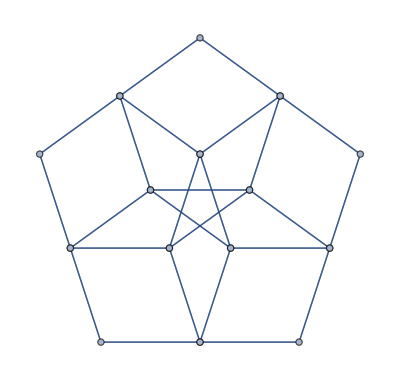

```mathematica
G=GraphProduct[GraphData[{"Cycle",5}],GraphData[{"Cycle",5}]]
```

```mathematica
G=Graph[{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10,5<->11,5<->12,6<->13,6<->14,7<->15,7<->16,8<->17,8<->18,9<->19,9<->20,10<->21,10<->22,11<->17,11<->19,12<->20,12<->22,13<->21,13<->23,14<->15,14<->24,15<->12,16<->23,16<->18,17<->24,18<->5,19<->14,20<->7,21<->9,22<->1,23<->2,24<->6},VertexLabels->"Name",GraphStyle->"SmallNetwork"];

(*Display the graph*)
GraphPlot[G]
```

-Graphics-

```mathematica
c=0; A=AdjacencyMatrix[G]; Y=Table[Table[If[i≥j &&A[[i,j]]==1, c++;x[c],0],{i,1,VertexCount[G]}],{j,1,VertexCount[G]}]; Y=Y+Transpose[Y]; For[i=1, i≤VertexCount[G],i++,Y[[i,i]]=Y[[i,i]]/2]; 
vars=Union[Flatten[Y]]; vars[[1]]=x[0]; vars =Drop[vars,1] ;
matlist={};For[i=1, i≤Length[vars],i++ , ttt =  CoefficientList[Y,vars[[i]]]; tttt=Table[Table[If[Length[ttt[[s,t]]]==2,1,0],{s,1,VertexCount[G]}],{t,1,VertexCount[G]}]; AppendTo[matlist, tttt]];matlist=PrependTo[matlist, Table[Table[0,{VertexCount[G]}],{VertexCount[G]}]]; matlist[[1]]=IdentityMatrix[VertexCount[G]];
For[i=1, i<=Length[matlist],i++,  For[j=1, j<=Length[matlist[[i]]],j++, matlist[[i,j,j]]= - Plus@@matlist[[i,j]]]];For[i=1, i<=Length[matlist],i++,matlist[[i]]=-matlist[[i]]];
cons={Sum[vars[[k]]matlist[[k+1]],{k,1,Length[vars]}]  +Table[Table[1,{VertexCount[G]}],{VertexCount[G]}]/VertexCount[G] -IdentityMatrix[VertexCount[G]](\[VectorGreaterEqual])_ 0};
cons2=Table[ vars[[s]]>=0,{s,1,Length[vars]}];
semi=SemidefiniteOptimization[Plus@@vars, {cons,cons2},vars];weights= vars/.semi; Ki=KirchhoffMatrix[G]; Ki=Ki/Eigenvalues[Ki][[-2]]; Ki=Ki-DiagonalMatrix[Diagonal[Ki]]; flat=-Plus@@Flatten[Ki] ; M=Sum[vars[[k]]matlist[[k+1]],{k,1,Length[vars]}]/.semi;  Ki=M; Ki=Ki-DiagonalMatrix[Diagonal[Ki]]; new=-Plus@@Flatten[Ki]; one=N[{flat,new}]; 

cons={(-Sum[vars[[k]]matlist[[k+1]],{k,1,Length[vars]}] + IdentityMatrix[VertexCount[G]])(\[VectorGreaterEqual])_ 0};
cons2=Table[ vars[[s]]>=0,{s,1,Length[vars]}];
semi=SemidefiniteOptimization[-Plus@@vars, {cons,cons2},vars];
Ki=KirchhoffMatrix[G]; Ki=Ki/Max[Eigenvalues[Ki]]; Ki=Ki-DiagonalMatrix[Diagonal[Ki]]; flat=Plus@@Flatten[Ki] ;
M=Sum[vars[[k]]matlist[[k+1]],{k,1,Length[vars]}]/.semi; Ki=M; Ki=Ki-DiagonalMatrix[Diagonal[Ki]]; new=Plus@@Flatten[Ki];two=N[-{flat, new}];


If[one[[2]]>=one[[1]]-0.0001 && two[[2]]<=two[[1]]+0.0001,Print[1]]
```

```mathematica
one[[2]]
```

83.5375

```mathematica
one[[1]]
```

111.531

```mathematica
two[[1]]
```

12.1081

```mathematica
two[[2]]
```

13.1916